```mathematica
Ts=0.1;
```

```mathematica
nmax = 60;
```

```mathematica
x[t_]:= Exp[-t^2];
```

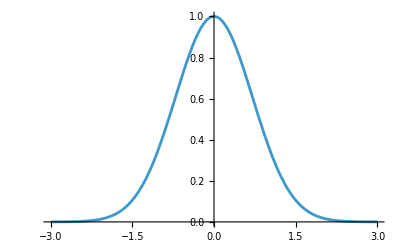

```mathematica
Plot[x[t],{t,-3,3}]
```

```mathematica
xSampled[t_]:= Sum[x[n*Ts]*DiracDelta[t-n*Ts],{n,-nmax,nmax}];
```

```mathematica
X[f_]= FourierTransform[xSampled[t] *Ts,t,f,FourierParameters->{0, -2*Pi}];
```

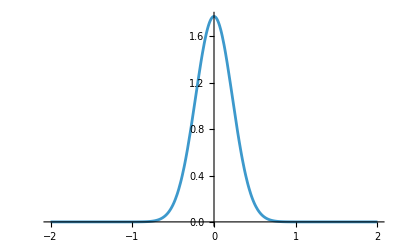

```mathematica
Plot[{Re[X[f]]},{f,-2,2},Exclusions->None]
```

```mathematica
f2=3;
```

```mathematica
xFiltered2[t_] = Integrate[X[f]*Exp[I*2Pi*f*t],{f,-f2,f2}];
```

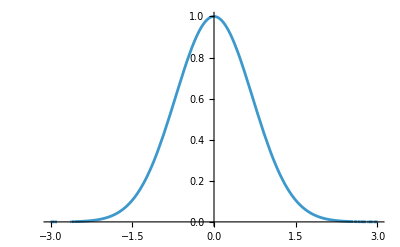

```mathematica
Plot[xFiltered2[t],{t,-3,3}]
```

```mathematica
Ts=0.3;
```

```mathematica
xSampled[t_]:= Sum[x[n*Ts]*DiracDelta[t-n*Ts],{n,-nmax,nmax}];
```

```mathematica
X[f_]= FourierTransform[xSampled[t] *Ts,t,f,FourierParameters->{0, -2*Pi}];
```

```mathematica
Plot[{Re[X[f]]},{f,-2,2},Exclusions->None]
```

-Graphics-

```mathematica
f2=3;
```

```mathematica
xFiltered2[t_] = Integrate[X[f]*Exp[I*2Pi*f*t],{f,-f2,f2}];
```

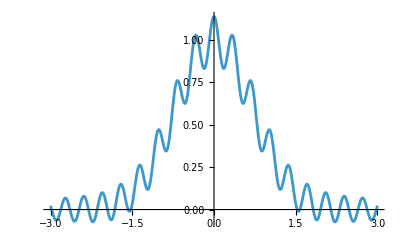

```mathematica
Plot[xFiltered2[t],{t,-3,3}]
```